## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`';
Get["MASSef`"];
Get["MASSef`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="TALA2";
fitLabel=rxnName;
dataFileName=rxnName;
KeqEquilibrator=1/1.19;

assumedUncertaintyFraction = 0.05;
removeInputFiles = False;
removeOutputFiles = True;
(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/test bla/MASSef/";

mainFolder = "fit_dKd_GAPD";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath, assumedUncertaintyFraction];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(e4p^c+f6p^c⇌g3p^c+s7p^c)^TALA2

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Km Values:

Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
g3p | 0.000038 | 0.0000361
0.0000399 | f6p | 0.0285 | M | 8.5 | 30 | glygly | 0.05 | 
e4p | 0.00009 | 0.0000855
0.0000945 | f6p | 0.0285 | M | 8.5 | 30 | glygly | 0.05 | 
r5p | 0.031 | 0.02945
0.03255 | f6p | 0.0285 | M | 8.5 | 30 | glygly | 0.05 | 
f6p | 0.0012 | 0.00114
0.00126 | g3p | 0.0038 | M | 8.5 | 30 | glygly | 0.05 | 
s7p | 0.000285 | 0.00027075
0.00029925 | g3p | 0.0038 | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
f6p | Null
e4p | 0.002 | 71.4 | 67.83
74.97 | 1/s | 8.5 | 30 | glygly | 0.05 | 
e4p | Null
f6p | 0.05 | 79.4 | 75.43
83.37 | 1/s | 8.5 | 30 | glygly | 0.05 |

Inhibition Values:

Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Kic | pi | 0.019 | 0.016
0.022 | e4p | Null | Competitive | Null | Null | f6p | Null | M | 8.5 | 30 | glygly | 0.05 | 
Kic | pi | 0.019 | 0.016
0.022 | f6p | Null | Competitive | Null | Null | e4p | Null | M | 8.5 | 30 | glygly | 0.05 | 
Kic | pi | 0.019 | 0.016
0.022 | g3p | Null | Competitive | Null | Null | s7p | Null | M | 8.5 | 30 | glygly | 0.05 | 
Kic | pi | 0.019 | 0.016
0.022 | s7p | Null | Competitive | Null | Null | g3p | Null | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

{8.5,30.}

```mathematica
kmList
```

{{g3p,0.000038,{0.0000361,0.0000399},{{f6p,0.0285}},M,8.5,30,{{glygly,0.05}},{}},{e4p,0.00009,{0.0000855,0.0000945},{{f6p,0.0285}},M,8.5,30,{{glygly,0.05}},{}},{r5p,0.031,{0.02945,0.03255},{{f6p,0.0285}},M,8.5,30,{{glygly,0.05}},{}},{f6p,0.0012,{0.00114,0.00126},{{g3p,0.0038}},M,8.5,30,{{glygly,0.05}},{}},{s7p,0.000285,{0.00027075,0.00029925},{{g3p,0.0038}},M,8.5,30,{{glygly,0.05}},{}}}

```mathematica
kcatList
```

{{{{f6p,Null},{e4p,0.002}},71.4,{67.83,74.97},1/s,8.5,30,{{glygly,0.05}},{}},{{{e4p,Null},{f6p,0.05}},79.4,{75.43,83.37},1/s,8.5,30,{{glygly,0.05}},{}}}

```mathematica
inhibitionList
```

{{Kic,pi,0.019,{0.016,0.022},{{e4p,Null}},{{Competitive,Null,Null,f6p,Null}},M,8.5,30,{{glygly,0.05}},{}},{Kic,pi,0.019,{0.016,0.022},{{f6p,Null}},{{Competitive,Null,Null,e4p,Null}},M,8.5,30,{{glygly,0.05}},{}},{Kic,pi,0.019,{0.016,0.022},{{g3p,Null}},{{Competitive,Null,Null,s7p,Null}},M,8.5,30,{{glygly,0.05}},{}},{Kic,pi,0.019,{0.016,0.022},{{s7p,Null}},{{Competitive,Null,Null,g3p,Null}},M,8.5,30,{{glygly,0.05}},{}}}

### Construct enzyme module

```mathematica
{{"Ping Pong Bi Bi"}, {"\"[f6p,g3p,e4p,s7p]\""}}
```

```mathematica
catalyticBranch={"E_TALA2[c] + f6p[c] <=> E_TALA2[c]&f6p",
				"E_TALA2[c]&f6p <=> E_TALA2[c]&mod&g3p",
				"E_TALA2[c]&mod&g3p <=> E_TALA2[c]&mod + g3p[c]",
                                      "E_TALA2[c]&mod + e4p[c] <=> E_TALA2[c]&mod&e4p",
				"E_TALA2[c]&mod&e4p <=> E_TALA2[c]&s7p",
				"E_TALA2[c]&s7p <=> E_TALA2[c] + s7p[c]"};





enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
```

### Setup King-Altmann Equations

```mathematica
{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};


{enzymeModel, nonCatalyticReactions} =addInhibitionReactions[enzymeModel, rxnName, inhibitionList[[{1,2}]],  allCatalyticReactions, nonCatalyticReactions];
nonCatalyticReactions//TableForm

(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs];

eqRateConstSub={};
(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getEquivRateConsts[enzymeModel, eqRateConstSub, nonCatalyticReactions];


(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];

(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];
```

((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p
((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p

## Semi-Automated Simulate Data

### User Input Section

```mathematica
logStepSize=0.2;
(*nonKmParamWeight=3;*)
(*Weighting factor for non-Km data points. You can be specify this manually*)
{minPsDataVal, maxPsDataVal}= getMinMaxPsDataVal[1];
nonKmParamWeight=Length[Table[1,{i,minPsDataVal, maxPsDataVal,logStepSize}]];
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)

pHandT = kmList[[1]][[{5,6}]];
```

### Simulate data

```mathematica
pHandT={8.5, 30};

kmFittingData= simulateKmData[rxn, metsFull,  metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			   logStepSize,activeIsoSub, bufferInfo, ionCharge, inputPath,  fileList, KeqEquilibrator];

kcatFittingData=simulateKcatData[rxn, metsFull,  metSatForSub, metSatRevSub, kcatList, otherParmsList, assumedSaturatingConc, eTotal,
			  logStepSize, nonKmParamWeight, activeIsoSub, bufferInfo, ionCharge, inputPath, 
			   fileList, KeqEquilibrator];

haldane=haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneRatio=haldane[[2]];

{KeqFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[haldaneRatio,KeqEquilibrator, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT,"haldaneRatio"];

dKdVal =125.79;
dKdRatio =( Subscript[k, TALA21]^⟶/Subscript[k, TALA21]^⟵)*(Subscript[k, TALA22]^⟶/Subscript[k, TALA22]^⟵);

{dKdFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[dKdRatio,dKdVal, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, eqnName="dKdRatio"];

inhibVal =inhibitionList[[1]][[3]];
inhibRatio =Subscript[k, TALA2_Kic_pi_1_f6p_TALA2_Kic_pi_1_e4p]^⟵/Subscript[k, TALA2_Kic_pi_1_f6p_TALA2_Kic_pi_1_e4p]^⟶;

{inhibRatioFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[inhibRatio,inhibVal, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, eqnName="inhibRatio"];

logStepSize=0.2;
inhibFittingData=simulateInhibData[rxn, metsFull, metSatForSub, metSatRevSub,  inhibitionList, kmList, assumedSaturatingConc, eTotal,
			   logStepSize, activeIsoSub, bufferInfo, ionCharge, inputPath, fileList, KeqEquilibrator];
```

{0.0166535,0.0166535,0.0166535,0.0166535}

#### sanity check plots

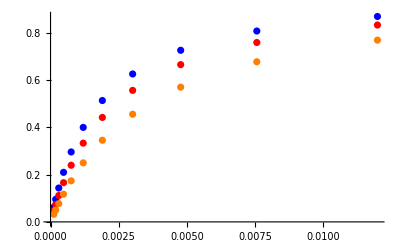

```mathematica
inhib1=inhibFittingData[[1;;11,{3,-1}]];
inhib2=inhibFittingData[[12;;22,{3,-1}]];
inhib3=inhibFittingData[[23;;33,{3,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.0018}

{1.,0.0024}

{1.,0.0036}

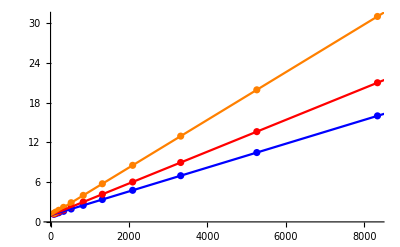

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,0,10000}, PlotStyle->{Blue,Red, Orange}]]
```

### Assemble and export All Data

```mathematica
header=Join[Map[ToString, metsSub[[All,1]]],{"FileFlag", "Target_Data"}];
fittingData = Flatten[{kmFittingData,kcatFittingData,KeqFittingData,dKdFittingData, inhibRatioFittingData,inhibFittingData}, 1];

dataPath =FileNameJoin[{inputPath,dataFileName <>".dat"}, OperatingSystem->$OperatingSystem];

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
FilePrint[dataPath]
```

Keq_TALA2	e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
0.8403361344537815	0	0	3.7999999999999996e-6	0.01	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_g3p.txt"	0.09090909090909091
0.8403361344537815	0	0	6.022594131352233e-6	0.01	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_g3p.txt"	0.13680688860321005
0.8403361344537815	0	0	9.545168439736411e-6	0.01	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_g3p.txt"	0.20076000891310186
0.8403361344537815	0	0	0.000015128072481032882	0.01	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_g3p.txt"	0.2847472489508012
0.8403361344537815	0	0	0.00002397637909024733	0.01	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_g3p.txt"	0.3868631798468568
0.8403361344537815	0	0	0.000037999999999999995	0.01	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_g3p.txt"	0.49999999999999994
0.8403361344537815	0	0	0.000060225941313522335	0.01	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_g3p.txt"	0.6131368201531431
0.8403361344537815	0	0	0.00009545168439736412	0.01	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_g3p.txt"	0.7152527510491987
0.8403361344537815	0	0	0.00015128072481032897	0.01	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_g3p.txt"	0.7992399910868984
0.8403361344537815	0	0	0.0002397637909024733	0.01	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_g3p.txt"	0.86319311139679
0.8403361344537815	0	0	0.00037999999999999997	0.01	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_g3p.txt"	0.9090909090909091
0.8403361344537815	9.000000000000007e-6	0.0285	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_e4p.txt"	0.09090909090909098
0.8403361344537815	0.000014264038732150038	0.0285	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_e4p.txt"	0.13680688860321014
0.8403361344537815	0.000022606977883586257	0.0285	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_e4p.txt"	0.20076000891310197
0.8403361344537815	0.00003582964534981475	0.0285	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_e4p.txt"	0.2847472489508014
0.8403361344537815	0.00005678616100321741	0.0285	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_e4p.txt"	0.38686317984685703
0.8403361344537815	0.00009000000000000007	0.0285	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_e4p.txt"	0.5000000000000002
0.8403361344537815	0.00014264038732150037	0.0285	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_e4p.txt"	0.6131368201531432
0.8403361344537815	0.00022606977883586258	0.0285	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_e4p.txt"	0.7152527510491988
0.8403361344537815	0.00035829645349814786	0.0285	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_e4p.txt"	0.7992399910868985
0.8403361344537815	0.0005678616100321741	0.0285	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_e4p.txt"	0.86319311139679
0.8403361344537815	0.0009000000000000007	0.0285	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_e4p.txt"	0.9090909090909093
0.8403361344537815	0.01	0.00011999999999999995	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_f6p.txt"	0.09090909090909088
0.8403361344537815	0.01	0.00019018718309533363	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_f6p.txt"	0.13680688860321
0.8403361344537815	0.01	0.0003014263717811494	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_f6p.txt"	0.20076000891310164
0.8403361344537815	0.01	0.0004777286046641966	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_f6p.txt"	0.28474724895080133
0.8403361344537815	0.01	0.0007571488133762321	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_f6p.txt"	0.38686317984685703
0.8403361344537815	0.01	0.0011999999999999995	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_f6p.txt"	0.49999999999999994
0.8403361344537815	0.01	0.0019018718309533362	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_f6p.txt"	0.613136820153143
0.8403361344537815	0.01	0.0030142637178114944	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_f6p.txt"	0.7152527510491984
0.8403361344537815	0.01	0.004777286046641966	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_f6p.txt"	0.7992399910868982
0.8403361344537815	0.01	0.007571488133762321	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_f6p.txt"	0.8631931113967899
0.8403361344537815	0.01	0.011999999999999995	0	0	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateFor_f6p.txt"	0.9090909090909092
0.8403361344537815	0	0	0.0038	0.0000285	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_s7p.txt"	0.09090909090909093
0.8403361344537815	0	0	0.0038	0.000045169455985141756	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_s7p.txt"	0.13680688860321005
0.8403361344537815	0	0	0.0038	0.00007158876329802309	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_s7p.txt"	0.2007600089131019
0.8403361344537815	0	0	0.0038	0.00011346054360774674	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_s7p.txt"	0.28474724895080145
0.8403361344537815	0	0	0.0038	0.000179822843176855	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_s7p.txt"	0.38686317984685686
0.8403361344537815	0	0	0.0038	0.000285	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_s7p.txt"	0.5
0.8403361344537815	0	0	0.0038	0.00045169455985141755	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_s7p.txt"	0.6131368201531432
0.8403361344537815	0	0	0.0038	0.000715887632980231	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_s7p.txt"	0.7152527510491988
0.8403361344537815	0	0	0.0038	0.0011346054360774674	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_s7p.txt"	0.7992399910868982
0.8403361344537815	0	0	0.0038	0.00179822843176855	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_s7p.txt"	0.86319311139679
0.8403361344537815	0	0	0.0038	0.00285	0.01	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\relRateRev_s7p.txt"	0.9090909090909091
0.8403361344537815	0.002	0.01	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	71.4
0.8403361344537815	0.002	0.01	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	71.4
0.8403361344537815	0.002	0.01	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	71.4
0.8403361344537815	0.002	0.01	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	71.4
0.8403361344537815	0.002	0.01	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	71.4
0.8403361344537815	0.002	0.01	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	71.4
0.8403361344537815	0.002	0.01	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	71.4
0.8403361344537815	0.002	0.01	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	71.4
0.8403361344537815	0.002	0.01	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	71.4
0.8403361344537815	0.002	0.01	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	71.4
0.8403361344537815	0.002	0.01	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	71.4
0.8403361344537815	0.01	0.05	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	79.4
0.8403361344537815	0.01	0.05	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	79.4
0.8403361344537815	0.01	0.05	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	79.4
0.8403361344537815	0.01	0.05	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	79.4
0.8403361344537815	0.01	0.05	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	79.4
0.8403361344537815	0.01	0.05	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	79.4
0.8403361344537815	0.01	0.05	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	79.4
0.8403361344537815	0.01	0.05	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	79.4
0.8403361344537815	0.01	0.05	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	79.4
0.8403361344537815	0.01	0.05	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	79.4
0.8403361344537815	0.01	0.05	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	79.4
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\haldaneRatio.txt"	0.8403361344537815
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\haldaneRatio.txt"	0.8403361344537815
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\haldaneRatio.txt"	0.8403361344537815
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\haldaneRatio.txt"	0.8403361344537815
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\haldaneRatio.txt"	0.8403361344537815
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\haldaneRatio.txt"	0.8403361344537815
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\haldaneRatio.txt"	0.8403361344537815
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\haldaneRatio.txt"	0.8403361344537815
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\haldaneRatio.txt"	0.8403361344537815
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\haldaneRatio.txt"	0.8403361344537815
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\haldaneRatio.txt"	0.8403361344537815
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\dKdRatio.txt"	125.79
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\dKdRatio.txt"	125.79
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\dKdRatio.txt"	125.79
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\dKdRatio.txt"	125.79
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\dKdRatio.txt"	125.79
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\dKdRatio.txt"	125.79
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\dKdRatio.txt"	125.79
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\dKdRatio.txt"	125.79
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\dKdRatio.txt"	125.79
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\dKdRatio.txt"	125.79
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\dKdRatio.txt"	125.79
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\inhibRatio.txt"	0.019
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\inhibRatio.txt"	0.019
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\inhibRatio.txt"	0.019
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\inhibRatio.txt"	0.019
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\inhibRatio.txt"	0.019
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\inhibRatio.txt"	0.019
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\inhibRatio.txt"	0.019
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\inhibRatio.txt"	0.019
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\inhibRatio.txt"	0.019
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\inhibRatio.txt"	0.019
0.8403361344537815	0	0	0	0	0	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\inhibRatio.txt"	0.019
0.8403361344537815	0.01	0.00011999999999999995	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.06249999999999998
0.8403361344537815	0.01	0.00019018718309533363	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.09556246000918162
0.8403361344537815	0.01	0.0003014263717811494	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.1434389402497425
0.8403361344537815	0.01	0.0004777286046641966	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.2097390372522576
0.8403361344537815	0.01	0.0007571488133762321	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.2960910250571456
0.8403361344537815	0.01	0.0011999999999999995	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.3999999999999999
0.8403361344537815	0.01	0.0019018718309533362	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.5137595027063783
0.8403361344537815	0.01	0.0030142637178114944	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.6261110513450937
0.8403361344537815	0.01	0.004777286046641966	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.7263308928279026
0.8403361344537815	0.01	0.007571488133762321	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.8079280500270597
0.8403361344537815	0.01	0.011999999999999995	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.8695652173913043
0.8403361344537815	0.01	0.00011999999999999995	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.0476190476190476
0.8403361344537815	0.01	0.00019018718309533363	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.07342603821707416
0.8403361344537815	0.01	0.0003014263717811494	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.11158045058337385
0.8403361344537815	0.01	0.0004777286046641966	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.16600891546544677
0.8403361344537815	0.01	0.0007571488133762321	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.2398204386718606
0.8403361344537815	0.01	0.0011999999999999995	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.33333333333333326
0.8403361344537815	0.01	0.0019018718309533362	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.44210332285326664
0.8403361344537815	0.01	0.0030142637178114944	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.5567264313142644
0.8403361344537815	0.01	0.004777286046641966	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.6656117668428602
0.8403361344537815	0.01	0.007571488133762321	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.7593137586080182
0.8403361344537815	0.01	0.011999999999999995	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.8333333333333333
0.8403361344537815	0.01	0.00011999999999999995	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.03225806451612902
0.8403361344537815	0.01	0.00019018718309533363	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.05017883653440393
0.8403361344537815	0.01	0.0003014263717811494	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.07726055628304394
0.8403361344537815	0.01	0.0004777286046641966	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.11715556648810813
0.8403361344537815	0.01	0.0007571488133762321	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.17377162126109225
0.8403361344537815	0.01	0.0011999999999999995	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.2499999999999999
0.8403361344537815	0.01	0.0019018718309533362	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.34567723301976483
0.8403361344537815	0.01	0.0030142637178114944	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.455721732064358
0.8403361344537815	0.01	0.004777286046641966	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.5702665541135414
0.8403361344537815	0.01	0.007571488133762321	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.6777510787376546
0.8403361344537815	0.01	0.011999999999999995	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.769230769230769
0.8403361344537815	9.000000000000007e-6	0.01	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.06250000000000004
0.8403361344537815	0.000014264038732150038	0.01	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.09556246000918171
0.8403361344537815	0.000022606977883586257	0.01	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.14343894024974277
0.8403361344537815	0.00003582964534981475	0.01	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.2097390372522576
0.8403361344537815	0.00005678616100321741	0.01	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.2960910250571456
0.8403361344537815	0.00009000000000000007	0.01	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.40000000000000013
0.8403361344537815	0.00014264038732150037	0.01	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.5137595027063786
0.8403361344537815	0.00022606977883586258	0.01	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.6261110513450943
0.8403361344537815	0.00035829645349814786	0.01	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.726330892827903
0.8403361344537815	0.0005678616100321741	0.01	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.8079280500270597
0.8403361344537815	0.0009000000000000007	0.01	0	0	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.8695652173913043
0.8403361344537815	9.000000000000007e-6	0.01	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.04761904761904766
0.8403361344537815	0.000014264038732150038	0.01	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.07342603821707423
0.8403361344537815	0.000022606977883586257	0.01	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.11158045058337406
0.8403361344537815	0.00003582964534981475	0.01	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.16600891546544674
0.8403361344537815	0.00005678616100321741	0.01	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.2398204386718606
0.8403361344537815	0.00009000000000000007	0.01	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.33333333333333354
0.8403361344537815	0.00014264038732150037	0.01	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.4421033228532669
0.8403361344537815	0.00022606977883586258	0.01	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.5567264313142649
0.8403361344537815	0.00035829645349814786	0.01	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.6656117668428604
0.8403361344537815	0.0005678616100321741	0.01	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.7593137586080181
0.8403361344537815	0.0009000000000000007	0.01	0	0	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.8333333333333336
0.8403361344537815	9.000000000000007e-6	0.01	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.03225806451612906
0.8403361344537815	0.000014264038732150038	0.01	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.050178836534403984
0.8403361344537815	0.000022606977883586257	0.01	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.0772605562830441
0.8403361344537815	0.00003582964534981475	0.01	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.11715556648810813
0.8403361344537815	0.00005678616100321741	0.01	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.17377162126109227
0.8403361344537815	0.00009000000000000007	0.01	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.25000000000000017
0.8403361344537815	0.00014264038732150037	0.01	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.345677233019765
0.8403361344537815	0.00022606977883586258	0.01	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.45572173206435856
0.8403361344537815	0.00035829645349814786	0.01	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.5702665541135417
0.8403361344537815	0.0005678616100321741	0.01	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.6777510787376545
0.8403361344537815	0.0009000000000000007	0.01	0	0	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateFor.txt"	0.7692307692307694
0.8403361344537815	0	0	0.01	0.0000285	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.06250000000000001
0.8403361344537815	0	0	0.01	0.000045169455985141756	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.09556246000918166
0.8403361344537815	0	0	0.01	0.00007158876329802309	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.14343894024974266
0.8403361344537815	0	0	0.01	0.00011346054360774674	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.20973903725225762
0.8403361344537815	0	0	0.01	0.000179822843176855	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.29609102505714546
0.8403361344537815	0	0	0.01	0.000285	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.39999999999999997
0.8403361344537815	0	0	0.01	0.00045169455985141755	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.5137595027063785
0.8403361344537815	0	0	0.01	0.000715887632980231	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.626111051345094
0.8403361344537815	0	0	0.01	0.0011346054360774674	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.7263308928279029
0.8403361344537815	0	0	0.01	0.00179822843176855	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.8079280500270596
0.8403361344537815	0	0	0.01	0.00285	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.8695652173913043
0.8403361344537815	0	0	0.01	0.0000285	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.04761904761904762
0.8403361344537815	0	0	0.01	0.000045169455985141756	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.07342603821707419
0.8403361344537815	0	0	0.01	0.00007158876329802309	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.11158045058337397
0.8403361344537815	0	0	0.01	0.00011346054360774674	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.1660089154654468
0.8403361344537815	0	0	0.01	0.000179822843176855	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.23982043867186045
0.8403361344537815	0	0	0.01	0.000285	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.3333333333333333
0.8403361344537815	0	0	0.01	0.00045169455985141755	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.4421033228532668
0.8403361344537815	0	0	0.01	0.000715887632980231	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.5567264313142647
0.8403361344537815	0	0	0.01	0.0011346054360774674	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.6656117668428603
0.8403361344537815	0	0	0.01	0.00179822843176855	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.7593137586080182
0.8403361344537815	0	0	0.01	0.00285	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.8333333333333333
0.8403361344537815	0	0	0.01	0.0000285	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.03225806451612904
0.8403361344537815	0	0	0.01	0.000045169455985141756	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.05017883653440395
0.8403361344537815	0	0	0.01	0.00007158876329802309	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.07726055628304405
0.8403361344537815	0	0	0.01	0.00011346054360774674	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.11715556648810815
0.8403361344537815	0	0	0.01	0.000179822843176855	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.17377162126109214
0.8403361344537815	0	0	0.01	0.000285	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.25
0.8403361344537815	0	0	0.01	0.00045169455985141755	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.34567723301976483
0.8403361344537815	0	0	0.01	0.000715887632980231	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.45572173206435834
0.8403361344537815	0	0	0.01	0.0011346054360774674	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.5702665541135415
0.8403361344537815	0	0	0.01	0.00179822843176855	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.6777510787376545
0.8403361344537815	0	0	0.01	0.00285	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.7692307692307693
0.8403361344537815	0	0	3.7999999999999996e-6	0.01	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.062499999999999986
0.8403361344537815	0	0	6.022594131352233e-6	0.01	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.09556246000918163
0.8403361344537815	0	0	9.545168439736411e-6	0.01	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.14343894024974266
0.8403361344537815	0	0	0.000015128072481032882	0.01	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.20973903725225743
0.8403361344537815	0	0	0.00002397637909024733	0.01	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.29609102505714546
0.8403361344537815	0	0	0.000037999999999999995	0.01	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.3999999999999999
0.8403361344537815	0	0	0.000060225941313522335	0.01	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.5137595027063784
0.8403361344537815	0	0	0.00009545168439736412	0.01	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.626111051345094
0.8403361344537815	0	0	0.00015128072481032897	0.01	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.7263308928279028
0.8403361344537815	0	0	0.0002397637909024733	0.01	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.8079280500270596
0.8403361344537815	0	0	0.00037999999999999997	0.01	0.0095	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.8695652173913043
0.8403361344537815	0	0	3.7999999999999996e-6	0.01	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.04761904761904761
0.8403361344537815	0	0	6.022594131352233e-6	0.01	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.07342603821707418
0.8403361344537815	0	0	9.545168439736411e-6	0.01	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.11158045058337397
0.8403361344537815	0	0	0.000015128072481032882	0.01	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.1660089154654466
0.8403361344537815	0	0	0.00002397637909024733	0.01	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.23982043867186045
0.8403361344537815	0	0	0.000037999999999999995	0.01	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.33333333333333326
0.8403361344537815	0	0	0.000060225941313522335	0.01	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.4421033228532667
0.8403361344537815	0	0	0.00009545168439736412	0.01	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.5567264313142646
0.8403361344537815	0	0	0.00015128072481032897	0.01	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.6656117668428602
0.8403361344537815	0	0	0.0002397637909024733	0.01	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.759313758608018
0.8403361344537815	0	0	0.00037999999999999997	0.01	0.019	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.8333333333333334
0.8403361344537815	0	0	3.7999999999999996e-6	0.01	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.032258064516129024
0.8403361344537815	0	0	6.022594131352233e-6	0.01	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.050178836534403935
0.8403361344537815	0	0	9.545168439736411e-6	0.01	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.07726055628304404
0.8403361344537815	0	0	0.000015128072481032882	0.01	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.11715556648810803
0.8403361344537815	0	0	0.00002397637909024733	0.01	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.17377162126109214
0.8403361344537815	0	0	0.000037999999999999995	0.01	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.24999999999999997
0.8403361344537815	0	0	0.000060225941313522335	0.01	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.34567723301976483
0.8403361344537815	0	0	0.00009545168439736412	0.01	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.45572173206435834
0.8403361344537815	0	0	0.00015128072481032897	0.01	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.5702665541135415
0.8403361344537815	0	0	0.0002397637909024733	0.01	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.6777510787376545
0.8403361344537815	0	0	0.00037999999999999997	0.01	0.038	1	8.5	30	"C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\absRateRev.txt"	0.7692307692307692

## Configure the Particle Swarm Optimization

```mathematica
numFits=1;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	1
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	14
filesWithFunctions	[C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\absRateFor.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\absRateRev.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\relRateFor_e4p.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\relRateFor_f6p.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\relRateRev_g3p.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\relRateRev_s7p.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\haldaneRatio.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\dKdRatio.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\inhibRatio.txt]
data_file_name	C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\TALA2.dat
value_row	-1
function_row	-2
data_row_high	-2
summary_file_name	C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\output\raw\summary_TALA2.txt
ultimate_result_name	C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\output\raw\psoResults_TALA2.txt

## Configure the Levenberg-Marquardt Algorithm

```mathematica
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	14
candidates_import_path	C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\output\raw\psoResults_TALA2.txt
candidates_export_path	C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\output\raw\lmaResults_TALA2.txt
filesWithFunctions	[C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\absRateFor.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\absRateRev.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\relRateFor_e4p.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\relRateFor_f6p.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\relRateRev_g3p.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\relRateRev_s7p.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\haldaneRatio.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\dKdRatio.txt, C:\\Users\\mrama\\Desktop\\test bla\\MASSef\\examples\\fit_TALA2\\input\\inhibRatio.txt]
data_file_name	C:\Users\mrama\Desktop\test bla\MASSef\examples\fit_TALA2\input\TALA2.dat
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python","\""<>runFitScriptPath <>"\"", "\""<>psoParameterPath <>"\"", "\""<>lmaParameterPath <>"\"", "\""<>psoTrialSummaryFileName <>"\"","\""<> psoResultsFileName <>"\"", "\""<>lmaResultsFileName <>"\"", ToString @numFits, "\""<>dataPath <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"]
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
fittingData = Import[FileNameJoin[{inputPath, dataFileName<>".dat"}, OperatingSystem->$OperatingSystem]];
fittingData = fittingData[[2;;,All]];
resultsFile = FileNameJoin[{"raw","lmaResults_"<> fitLabel<> ".txt"}, OperatingSystem->$OperatingSystem];
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,fitLabel];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Relative error | True value | Predicted Value
 |  |  | 
relRateFor_2pg | 5.98273×10^-10 | 0.0909091 | 0.0909091
relRateFor_2pg | 5.68088×10^-10 | 0.136807 | 0.136807
relRateFor_2pg | 5.25982×10^-10 | 0.20076 | 0.20076
relRateFor_2pg | 4.70724×10^-10 | 0.284747 | 0.284747
relRateFor_2pg | 4.03524×10^-10 | 0.386863 | 0.386863
relRateFor_2pg | 3.29048×10^-10 | 0.5 | 0.5
relRateFor_2pg | 2.54606×10^-10 | 0.613137 | 0.613137
relRateFor_2pg | 1.87414×10^-10 | 0.715253 | 0.715253
relRateFor_2pg | 1.32117×10^-10 | 0.79924 | 0.79924
relRateFor_2pg | 9.00327×10^-11 | 0.863193 | 0.863193
relRateFor_2pg | 5.98166×10^-11 | 0.909091 | 0.909091
haldaneRatio | 8.15567×10^-10 | 5.19 | 5.19
haldaneRatio | 8.15567×10^-10 | 5.19 | 5.19
haldaneRatio | 8.15567×10^-10 | 5.19 | 5.19
haldaneRatio | 8.15567×10^-10 | 5.19 | 5.19
haldaneRatio | 8.15567×10^-10 | 5.19 | 5.19
haldaneRatio | 8.15567×10^-10 | 5.19 | 5.19
haldaneRatio | 8.15567×10^-10 | 5.19 | 5.19
haldaneRatio | 8.15567×10^-10 | 5.19 | 5.19
haldaneRatio | 8.15567×10^-10 | 5.19 | 5.19
haldaneRatio | 8.15567×10^-10 | 5.19 | 5.19
haldaneRatio | 8.15567×10^-10 | 5.19 | 5.19
dKdRatio | 8.78186×10^-12 | 0.25 | 0.25
dKdRatio | 8.78186×10^-12 | 0.25 | 0.25
dKdRatio | 8.78186×10^-12 | 0.25 | 0.25
dKdRatio | 8.78186×10^-12 | 0.25 | 0.25
dKdRatio | 8.78186×10^-12 | 0.25 | 0.25
dKdRatio | 8.78186×10^-12 | 0.25 | 0.25
dKdRatio | 8.78186×10^-12 | 0.25 | 0.25
dKdRatio | 8.78186×10^-12 | 0.25 | 0.25
dKdRatio | 8.78186×10^-12 | 0.25 | 0.25
dKdRatio | 8.78186×10^-12 | 0.25 | 0.25
dKdRatio | 8.78186×10^-12 | 0.25 | 0.25

### Simulated Data and Best Fit Data Plot

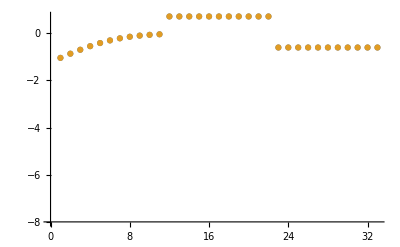

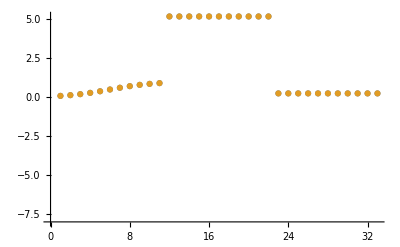

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

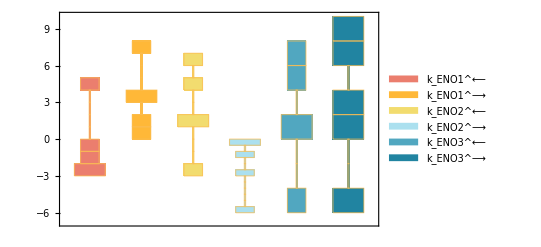

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

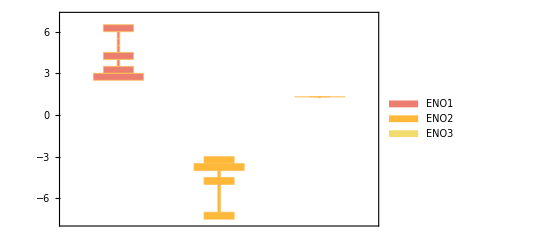

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

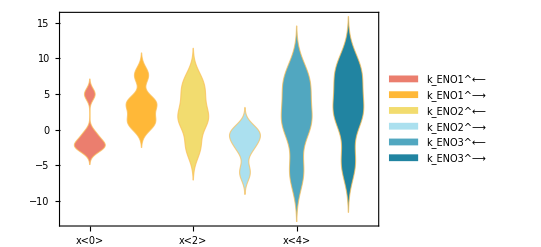

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[inputPath  <> "(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}];
```

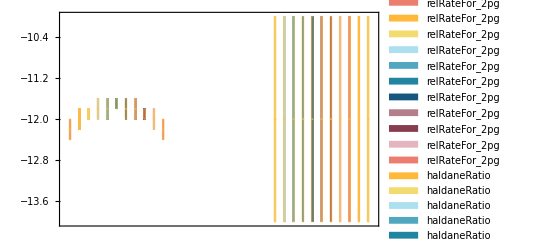

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> eTotal;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.0001 | 0.0001 | 6.58111×10^-10

```mathematica
backCalculateRatios[dKdRatio, dKdVal, paramFitSub]//TableForm
```

data value | predicted value | error in %
0.25 | 0.25 | 8.78186×10^-12

```mathematica
backCalculateRatios[haldaneRatio, KeqEquilibrator, paramFitSub]//TableForm
```

data value | predicted value | error in %
5.19 | 5.19 | 8.15567×10^-10